```mathematica
saveTransferFunction[peaks_,intensity0_,alpha0_,rgb_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xmlobject,rangeOfAlpha,index0,alpha2,rgba255},
index0=Flatten@Position[alpha0,_?(#>0&)];
rangeOfAlpha=Range[Length[alpha0]];
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha2[[#]]]&/@rangeOfAlpha;
rgba255=Transpose[rgb~Join~{a2}];
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@rgba255//(RGBColor/@#&);
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)
xrgba=Table[Join[{intensity2[[i]]},rgba255[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xmlobject=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function created using Wolfram Mathematica"]},VoreenData,{}];
Export[filename,xmlobject, "XML"];
rgbafunction2
]
```

```mathematica
SlicerXML[filename_]:=Module[{tf,list,x,r,g,b,rgb,intensity,colors},
tf=Import[filename];
list=ToExpression/@(StringSplit@First@Cases[tf,XMLElement["VolumeProperty",{___,"colorTransfer"->atrib_,___},___]:>atrib,∞]);
{x,r,g,b}=Transpose@Partition[list[[2;;]],4];
rgb=Transpose@{r,g,b};
intensity=Rescale[x,{Min[x],Max[x]}];
colors=RGBColor/@rgb;
Blend[Transpose@{intensity,colors},#]&
]
```

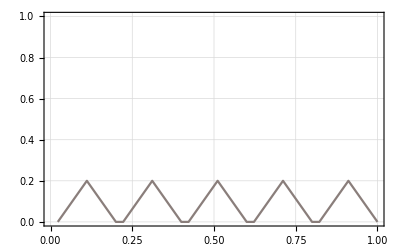
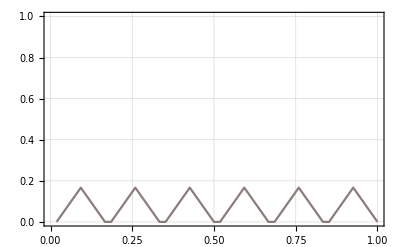
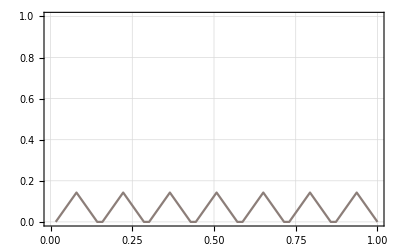
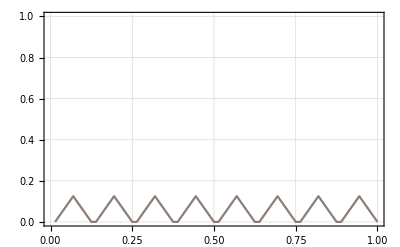
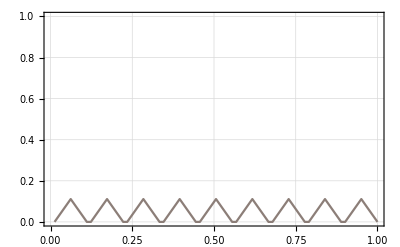
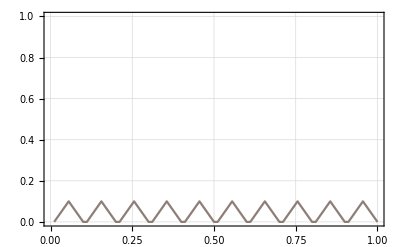
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
typestr={"_even","_diagonal"};
type=1;(* 1 for even, 2 for diagonal *)
range=Range[2,10];
path=NotebookDirectory[]<>"run\\";
colorindex=3;
colorname={"CT-Bone","CT-Chest-Vessels","Rainbow"}[[colorindex]];
colormap=If[colorindex>2,ColorData[colorname],SlicerXML[NotebookDirectory[]<>"Slicer\\"<>colorname<>".xml"]];
Table[Module[{index,alpha0,intensity0,colors,reversedcolors,rgb,rgbfunction,peaks,peakindices,a1,a0},
(* the gap between peaks is 1/8 of peak width. e.g. control point indices for 2 peaks are {2,6,10,11,15,19} *)
index=Flatten@Table[{9i-7,9i-3,9i+1},{i,n}];
intensity0=Range[0,1,1./(9n)][[#]]&/@index;
a0=Table[If[Divisible[i+1,3],intensity0[[i]],0],{i,n*3}];
a1=Table[If[Divisible[i+1,3],1./n,0],{i,n*3}];
alpha0=If[type==1,a1,a0];
colors=colormap[#]&/@(Transpose@Partition[intensity0,3])[[2]]; (* colors for peaks *)
rgb=Transpose@Flatten[Table[{i,i,i},{i,IntegerPart[List@@#*255]&/@colors}],1];(* triple the colors *)
peakindices=Table[3i-1,{i,n}];
peaks=alpha0[[#]]&/@peakindices;
saveTransferFunction[peaks,intensity0,alpha0,rgb,path<>colorname<>ToString[n]<>typestr[[type]]<>".tfi"];
rgbfunction=(Blend[Transpose[{intensity0,RGBColor[#/255.]&/@Transpose[rgb]}], #1] & );
ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->colorname<>ToString[n],PlotTheme->"Detailed"]
],{n,range}]
```

```mathematica
dataname="CT-Knee";
d=Import["D:\\_data\\"<>dataname<>".tif","Image3D"];
Table[Module[{tf,intensity,r,g,b,a,rgbacolors,rgbafunction,img},
tf=Import[path<>colorname<>ToString[n]<>typestr[[type]]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbacolors=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgbacolors}], #1] & );
img=Image3D[d,ColorFunction->rgbafunction];
(*Export[NotebookDirectory[]<>"colortf\\"<>dataname<>"_"<>colorname<>ToString[n]<>".png",img];*)
],{n,range}];
```